# Cálculo de pârametros unitários de uma linha de transmissão

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2021/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=80 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito 138kV

Coordenadas dos condutores

```mathematica
xc={-10,0,10,-7,7};
yc={15,15,15,22,22};
```

Dados condutores de fase

```mathematica
rf=2.54*10^-2;
rint=8.03*10^-3;
Rdc=0.121*10^-3;
```

Dados dos cabos pararraios

```mathematica
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 0.5,PlotRange->{{-12,12},{5,30.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Função para cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
(* impedancia interna de condutores tubulares *)
ZintTubo[Omega_, Rhoc_, rf_, rint_, Mur_: 1, Mu_: (4.*Pi)/10^7] := 
 With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]], ri = rint + 10^-6}, 
  With[{Den = 
     BesselK[1, Etac*ri]*BesselI[1, Etac*rf] - 
      BesselK[1, Etac*rf]*BesselI[1, Etac*ri], 
    Num = BesselK[1, Etac*ri]*BesselI[0, Etac*rf] + 
      BesselK[0, Etac*rf]*BesselI[1, Etac*ri]}, ((Rhoc*Etac)*
      Num)/((2*Pi*rf)*Den)]]
      
(* impedancia interna de condutor sem alma de aco *)
(* impedancia interna de condutores cilindricos *) 
(*Mur=90 para cables de aco*)    
Zin[Omega_, Rhopr_, rpr_, Mur_:90, Mu_:(4*Pi)/10^7] := 
    With[{Etapr = Sqrt[(I*Omega*Mu*Mur)/Rhopr]}, 
         ((Etapr*Rhopr)*BesselI[0, Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]
```

```mathematica
(* internal impedance of cylindrical conductors *)
zintc= Compile[{{omega, _Complex}, {Rhoc, _Real}, {rf, _Real}, {ri,_Real}, {Mur, _Real}},
 ZintTubo[omega, Rhoc, rf, ri, Mur]];
 
zic= Compile[{{omega,_Complex},{rhoc, _Real},{rf, _Real}, {mur,_Real}},
	 Zin[omega, rhoc, rf, mur]];
```

```mathematica
(*  ground wires are not explicitly considered so we include their effects via Kron Reduction -- matrizes devem estar no formato de impedancia *)        
eliprc = Compile[{{m,_Complex,2},{nc,_Integer},{np,_Integer}},
	            Take[Inverse[m], nc - np, nc - np]
	            ];
```

```mathematica
(* case  2: ground wires and unbundled conductors *)
cZYlt[omega_,(x_)?VectorQ, (y_)?VectorQ, sigmas_, rdc_,rf_,rint_, npr_, rdcpr_, rpr_]:=
    Module[{mu=4*Pi*10^-7, eps=8.854*10^-12, nc=Length[x],  nf, rhoc, rhopr, mp, zin, ze, Z1, Y1},
    	
    nf= IntegerPart[(nc-npr)];
    rhoc= rdc*Pi*(rf^2-rint^2);
    rhopr= rdcpr*Pi*rpr^2;
   
   If[ rint != 0, 
   zin= DiagonalMatrix[
   	    Join[zintc[omega, rhoc, rf, rint, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr, 90] Table[1, {i, npr}]]
             ],
   zin= DiagonalMatrix[
   	    Join[zic[omega, rhoc, rf, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr,90] Table[1, {i, npr}]]
             ];
   ];
   
             
   ze= I omega mu/(2 Pi) With[{p = Sqrt[1/(I*omega*mu*sigmas)]}, 
         Table[If[i != j, 
         	  (Log[((x[[i]] - x[[j]])^2 + (2*p + y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 +(y[[i]] - y[[j]])^2)])/(2), 
              If[i <= nc - npr, 
               (Log[(2*(y[[i]] + p))/rf]), 
               (Log[(2*(y[[i]] + p))/rpr])]],
         {i, 1, nc}, 
         {j, 1, nc}]];
         
    Z1 = Inverse[eliprc[zin+ze, nc, npr]];     
         
    mp= Table[If[i != j, 
   	    (1/2)*Log[((x[[i]] - x[[j]])^2 + (y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 + (y[[i]] - y[[j]])^2)], 
        If[i <= nc - npr, Log[(2*y[[i]])/rf], 
        Log[(2*y[[i]])/rpr]]],{i, 1, nc}, {j, 1, nc}];
          
    Y1=3.0*10^-12 DiagonalMatrix[Table[1,{nf}]] + I omega*2*Pi*eps* eliprc[mp, nc, npr];
          
    {Z1, Y1}       
];
```

## Cálculo das matrizes

```mathematica
ω= 2. π 60;
ρs= 1000.;
npr = 2;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,rf,rint, npr, Rdcpr, rpr];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.222002+0.844766 ⅈ | 0.101534+0.377335 ⅈ | 0.0996032+0.326661 ⅈ
0.101534+0.377335 ⅈ | 0.224725+0.842161 ⅈ | 0.101534+0.377335 ⅈ
0.0996032+0.326661 ⅈ | 0.101534+0.377335 ⅈ | 0.222002+0.844766 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+3.15526×10^-6 ⅈ | 0.-3.81183×10^-7 ⅈ | 0.-1.18168×10^-7 ⅈ
0.-3.81183×10^-7 ⅈ | 3.×10^-9+3.21204×10^-6 ⅈ | 0.-3.81183×10^-7 ⅈ
0.-1.18168×10^-7 ⅈ | 0.-3.81183×10^-7 ⅈ | 3.×10^-9+3.15526×10^-6 ⅈ)

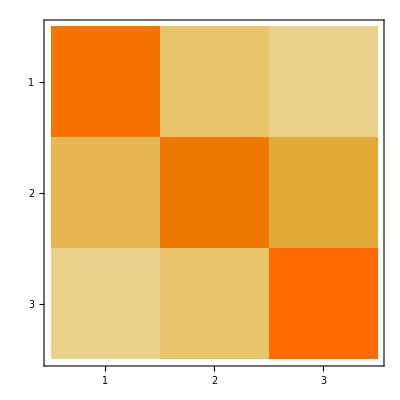

```mathematica
MatrixPlot[Abs@Zmat ]
```

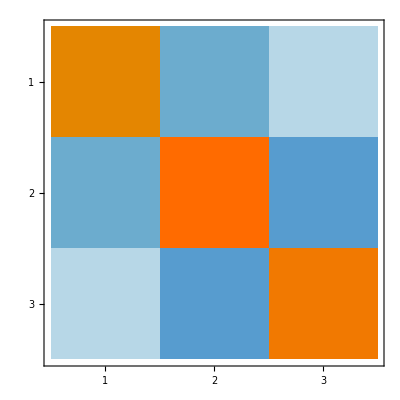

```mathematica
MatrixPlot[Im@Ymat ]
```

```mathematica
Zs = (Zmat[[1,1]]+Zmat[[2,2]]+Zmat[[3,3]])/3
```

0.00022291+0.000843897 ⅈ

```mathematica
Zm = (Zmat[[1,2]]+ Zmat[[1,3]]+Zmat[[2,3]])/3
```

0.00010089+0.000360443 ⅈ

```mathematica
Zabc = Table[If[i!= j, Zm, Zs],{i,1,3},{j,1,3}];
MatrixForm[Zabc 1000]
```

(0.22291+0.843897 ⅈ | 0.10089+0.360443 ⅈ | 0.10089+0.360443 ⅈ
0.10089+0.360443 ⅈ | 0.22291+0.843897 ⅈ | 0.10089+0.360443 ⅈ
0.10089+0.360443 ⅈ | 0.10089+0.360443 ⅈ | 0.22291+0.843897 ⅈ)

```mathematica
Ys = (Ymat[[1,1]]+Ymat[[2,2]]+Ymat[[3,3]])/3
```

3.×10^-12+3.17419×10^-9 ⅈ

```mathematica
Ym = (Ymat[[1,2]]+ Ymat[[1,3]]+Ymat[[2,3]])/3
```

0.-2.93511×10^-10 ⅈ

```mathematica
Yabc = Table[If[i!= j, Ym, Ys],{i,1,3},{j,1,3}];
MatrixForm[Yabc 1000]
```

(3.×10^-9+3.17419×10^-6 ⅈ | 0.-2.93511×10^-7 ⅈ | 0.-2.93511×10^-7 ⅈ
0.-2.93511×10^-7 ⅈ | 3.×10^-9+3.17419×10^-6 ⅈ | 0.-2.93511×10^-7 ⅈ
0.-2.93511×10^-7 ⅈ | 0.-2.93511×10^-7 ⅈ | 3.×10^-9+3.17419×10^-6 ⅈ)

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Z012= Inverse[A].Zabc. A;
MatrixForm[Z012*1000]
```

(0.42469+1.56478 ⅈ | -3.25261×10^-16-2.71051×10^-17 ⅈ | -3.25261×10^-16+0. ⅈ
8.13152×10^-17-1.35525×10^-16 ⅈ | 0.12202+0.483454 ⅈ | 0.+6.77626×10^-18 ⅈ
1.0842×10^-16-1.35525×10^-16 ⅈ | -2.71051×10^-17+4.06576×10^-17 ⅈ | 0.12202+0.483454 ⅈ)

```mathematica
MatrixForm[ 1000Inverse[A].Zmat.A]
```

(0.42469+1.56478 ⅈ | 0.0131007-0.00935492 ⅈ | -0.0146519-0.00666807 ⅈ
-0.0146519-0.00666807 ⅈ | 0.12202+0.483454 ⅈ | -0.0298187+0.0176538 ⅈ
0.0131007-0.00935492 ⅈ | 0.030198+0.0169968 ⅈ | 0.12202+0.483454 ⅈ)

```mathematica
Y012= Inverse[A].Yabc. A;
MatrixForm[Y012*1000]
```

(3.×10^-9+2.58717×10^-6 ⅈ | -1.03398×10^-22+4.1359×10^-22 ⅈ | 1.03398×10^-22+4.1359×10^-22 ⅈ
0.-3.10193×10^-22 ⅈ | 3.×10^-9+3.4677×10^-6 ⅈ | 0.-2.06795×10^-22 ⅈ
0.-3.10193×10^-22 ⅈ | 0.-2.06795×10^-22 ⅈ | 3.×10^-9+3.4677×10^-6 ⅈ)

```mathematica
Z0= Z012[[1,1]]*1000
```

0.42469+1.56478 ⅈ

```mathematica
Zpos= Z012[[2,2]]*1000
```

0.12202+0.483454 ⅈ

```mathematica
Ypos=Y012[[2,2]]*1000
```

3.×10^-9+3.4677×10^-6 ⅈ

```mathematica
Zc= Sqrt[Zpos/Ypos]
```

376.321-46.5917 ⅈ

```mathematica
Pn = 138^2/Zc
```

49.8418+6.17083 ⅈ

```mathematica
ℓ= 80.0;
Y1= 1/(Zpos ℓ) + Ypos ℓ;
Y2= -1/(Zpos ℓ);
 ZL= 376.32086209393407;
Y3= 1/ZL;
```

```mathematica
Yn={{Y1, Y2},{Y2, Y1+ Y3}};
MatrixForm@Yn
```

(0.00613517-0.0240298 ⅈ | -0.00613493+0.0243072 ⅈ
-0.00613493+0.0243072 ⅈ | 0.00879248-0.0240298 ⅈ)

```mathematica
Zn= Inverse[Yn];
MatrixForm@Zn
```

(377.679-40.1974 ⅈ | 363.975-77.4162 ⅈ
363.975-77.4162 ⅈ | 360.281-75.5967 ⅈ)

```mathematica
Vn=138./Sqrt[3]
```

79.6743

```mathematica
I1= Vn/Zn[[1,1]]1000
```

208.595+22.2013 ⅈ

```mathematica
V2=Zn[[2,1]] I1
```

77642.1-8067.9 ⅈ

```mathematica
V2 Sqrt[3]
```

134480.-13974. ⅈ

```mathematica
Arg[V2]/Degree
```

-5.93239

```mathematica
Abs[V2/(138 10^3/Sqrt[3])]
```

0.97974

```mathematica
IL= V2/ ZL
```

206.319-21.4389 ⅈ

```mathematica
3 10^-3 V2 Conjugate[IL]
```

48576.+0. ⅈ

```mathematica
V2a= 138 /Sqrt[3];
I2a= V2a/ZL;
```

```mathematica
a =1+ (Zpos ℓ) Ypos ℓ;
b =(Zpos ℓ);
c= A Ypos ℓ+  Ypos ℓ;
```

```mathematica
Q={{a,b},{c,a}};
MatrixForm[Q]
```

(0.989273+0.0027173 ⅈ | 9.76157+38.6763 ⅈ
-2.76396×10^-7+0.000551857 ⅈ | 0.989273+0.0027173 ⅈ)

```mathematica
sol=Q.{V2a, I2a}
```

{80.8864+8.40501 ⅈ,0.209426+0.0445441 ⅈ}

```mathematica
sol[[1]] Sqrt[3]/138
```

1.01521+0.105492 ⅈ

```mathematica
Arg[sol[[1]]]/Degree
```

5.93239

```mathematica
Q1={{1, (Zpos ℓ)},{0,1}};
MatrixForm[Q1]
```

(1 | 9.76157+38.6763 ⅈ
0 | 1)

```mathematica
sol1=Q1.{V2a, I2a}
```

{81.741+8.18851 ⅈ,0.211719+0. ⅈ}

```mathematica
Arg[sol1[[1]]]/Degree
```

5.72059